```mathematica
𝒟=NormalDistribution[100,16];
```

```mathematica
data=RandomVariate[𝒟,1000];
```

```mathematica
e𝒟=FindDistribution[data,TargetFunctions->{NormalDistribution}]
```

NormalDistribution[99.5148,16.2268]

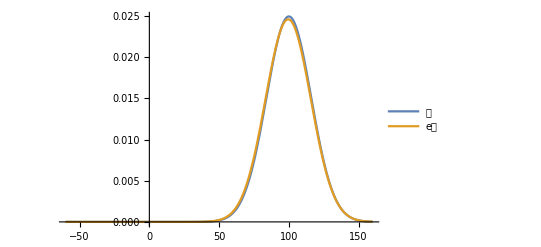

```mathematica
Plot[{PDF[𝒟,x],PDF[e𝒟,x]},{x,-60,160},PlotLegends->{"𝒟","e𝒟"},PlotRange->All]
```

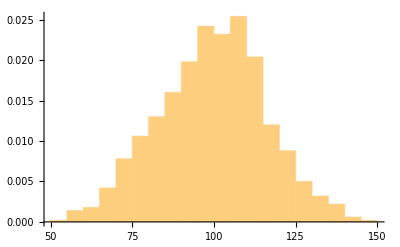

```mathematica
Show[Histogram[data,20,"ProbabilityDensity"],DiscretePlot[{PDF[e𝒟1,x]},{x,0,100}]]
```

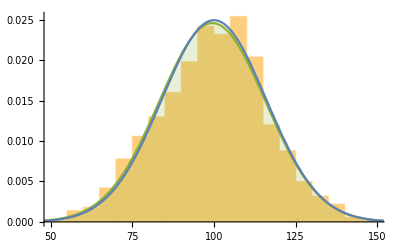

```mathematica
Show[Histogram[data,20,"ProbabilityDensity"],DiscretePlot[{PDF[e𝒟,x]},{x,0,160},PlotStyle->ColorData[97][3],Joined->True],Plot[{PDF[𝒟,x]},{x, 0, 160}]]
```